```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
{NN,RR} = Dimensions[S];
SubPlus[λ][ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];SubMinus[λ][ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
rates = {SubPlus[k][1]->1,SubMinus[k][1]->1,SubPlus[k][2]->1,SubMinus[k][2]->α,SubPlus[k][3]->4/3,SubMinus[k][3]->1}
J =Table[SubPlus[λ][ρ]- SubMinus[λ][ρ],{ρ,1,RR}];
J /.rates//MatrixForm
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→α,k_+[3]→4/3,k_-[3]→1}

(1-x[1]
-α x[1]+x[2]
-x[1]^3+4/3 x[1]^2 x[2])

```mathematica
A = S.J;A /.rates//MatrixForm
```

(1-x[1]-α x[1]-x[1]^3+x[2]+4/3 x[1]^2 x[2]
α x[1]+x[1]^3-x[2]-4/3 x[1]^2 x[2])

```mathematica
SubStar[x] = Solve[A == 0, Table[x[i],{i,1,NN}]][[1]];SubStar[x]/.rates //FullSimplify
```

{x[1]→1,x[2]→(3 (1+α))/7}

```mathematica
SubStar[vecx]=Table[x[i],{i,1,NN}]/. SubStar[x]/.rates
```

{1,(3 (1+α))/7}

```mathematica
SubStar[J]= J /. SubStar[x]; SubStar[J]/.rates//FullSimplify
```

{0,1/7 (3-4 α),1/7 (-3+4 α)}

```mathematica
Subscript[A, (1)] = Together@FullSimplify@Grad[A,{x[1],x[2]}]/. SubStar[x];Subscript[A, (1)]/.rates
```

{{-4-α+(8 (1+α))/7,7/3},{3+α-(8 (1+α))/7,-7/3}}

```mathematica
DD = FullSimplify[Det[Subscript[A, (1)]]]/.rates
```

7/3

```mathematica
T =FullSimplify[ Tr[Subscript[A, (1)]]]/.rates //Together
```

1/21 (-109+3 α)

```mathematica
Subscript[s, c]= Solve[T==0,α][[1]]//FullSimplify//Together;
Subscript[α, c]= Subscript[s, c][[1,2]]
```

10+9 β

```mathematica
Eigenvalues[Subscript[A, (1)]]/.rates/. Subscript[s, c] //FullSimplify
```

{-2 ⅈ,2 ⅈ}

```mathematica
Subscript[A, Δ]=A/.Table[x[i]->SubStar[vecx][[i]]+Δx[i],{i,1,NN}]/.rates;Collect[SubStar[A],{Δx[1],Δx[2]}]
```

{-x[1] k_-[1]-x[1] k_-[2]-x[1]^3 k_-[3]+k_+[1]+x[2] k_+[2]+x[1]^2 x[2] k_+[3],x[1] k_-[2]+x[1]^3 k_-[3]-x[2] k_+[2]-x[1]^2 x[2] k_+[3]}_*

```mathematica
γ=1/2
```

1/2

```mathematica
Subscript[A, δ]=(δα)^-γ Subscript[A, Δ]/. Δx[i_]->(δα)^γ δx[i]/.α -> Subscript[α, c]+δα//FullSimplify;Collect[Subscript[A, δ],δα]
```

{4 δx[1]+3/4 δα^(3/2) δx[1]^2+4 δx[2]+3/2 √δα δx[1] (5 δx[1]+4 δx[2])+1/2 δα δx[1] (1+6 δx[1] (-β δx[1]+δx[2])),-5 δx[1]-3/4 δα^(3/2) δx[1]^2-4 δx[2]+√δα (-15/2 δx[1]^2-6 δx[1] δx[2])+δα (-δx[1]/2+3 β δx[1]^3-3 δx[1]^2 δx[2])}

```mathematica
Subscript[M, 0]=Subscript[A, δ]/.δα->0//FullSimplify
```

{4 (δx[1]+δx[2]),-5 δx[1]-4 δx[2]}

```mathematica
Subscript[F, δ]=Subscript[A, δ]/.δx[i_]->δx[i][t];
```

```mathematica
par = {β->3,δα->0.1}
```

{β→3,δα→0.1}

```mathematica
EQS=Table[D[δx[i][t],t]==Subscript[F, δ][[i]],{i,1,NN}]/.par;EQS//MatrixForm
IC={δx[1][0]==10,δx[2][0]==10};
vars = Table[δx[i][t],{i,1,NN}];
```

(δx[1]'[t]==4 δx[2][t]+1/4 δx[1][t] (16+0.0948683 δx[1][t]+1.89737 (5 δx[1][t]+4 δx[2][t])+0.2 (1+6 δx[1][t] (-3 δx[1][t]+δx[2][t])))
δx[2]'[t]==0.9 (δx[1][t])^3-4 δx[2][t]-0.237171 (δx[1][t])^2 (10.1+1.26491 δx[2][t])-1/2 δx[1][t] (10.1+3.79473 δx[2][t]))

```mathematica
Subscript[t, max]=1000;
sols=NDSolve[{EQS,IC},vars,{t,0,Subscript[t, max]}][[1]]
```

{δx[1][t]→InterpolatingFunction[…][t],δx[2][t]→InterpolatingFunction[…][t]}

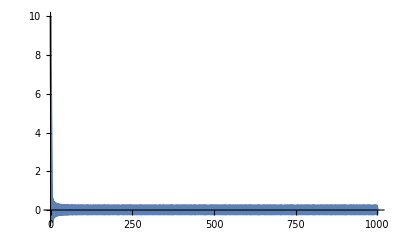

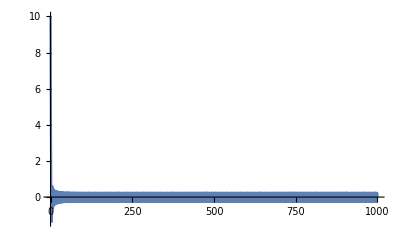

```mathematica
Plot[δx[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[δx[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

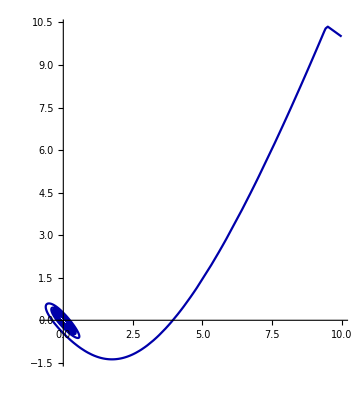

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

```mathematica
ee
```

ee

```mathematica
M = FullSimplify[Subscript[A, (1)]/.rates/.α->Subscript[α, c]];M//MatrixForm
```

(4 | 4
-5 | -4)

```mathematica
K = {{0,1},{1,0}};K//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
T=K.Inverse[Transpose[Eigenvectors[M]]];T//MatrixForm
```

(-ⅈ/4 | 1/10-ⅈ/5
ⅈ/4 | 1/10+ⅈ/5)

```mathematica
T.M.Inverse[T]//FullSimplify//MatrixForm
```

(-2 ⅈ | 0
0 | 2 ⅈ)

```mathematica
II = {{0,1},{-1,0}};II//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
U=Inverse[Transpose[Eigenvectors[II]]];U//MatrixForm
```

(ⅈ/2 | 1/2
-ⅈ/2 | 1/2)

```mathematica
U.II.Inverse[U]//FullSimplify//MatrixForm
```

(ⅈ | 0
0 | -ⅈ)

```mathematica
vecδy = Table[δy[i],{i,1,NN}]
```

{δy[1],δy[2]}

```mathematica
vecδx = Inverse[T].U.vecδy//FullSimplify/.β->(ω^2-1)
```

{-2 (δy[1]+2 δy[2]),5 δy[2]}

```mathematica
Subscript[A, δy]= FullSimplify@Subscript[A, δ]/.Table[δx[i]->vecδx[[i]],{i,1,NN}]
```

{20 δy[2]-1/2 (δy[1]+2 δy[2]) (16-6 δα^(3/2) (δy[1]+2 δy[2])+6 √δα (20 δy[2]-10 (δy[1]+2 δy[2]))+2 δα (1-12 (δy[1]+2 δy[2]) (5 δy[2]+2 β (δy[1]+2 δy[2])))),-20 δy[2]-24 β δα (δy[1]+2 δy[2])^3-3 √δα (δy[1]+2 δy[2])^2 (10+δα+20 √δα δy[2])+(δy[1]+2 δy[2]) (10+δα+60 √δα δy[2])}

```mathematica
V= Inverse[U].T.Subscript[A, δy]//FullSimplify
```

{-2 δy[2]-1/10 √δα (δy[1]+2 δy[2]) (30 δy[1]+√δα (-1+3 (δy[1]+2 δy[2]) (√δα+8 β δy[1]+4 (5+4 β) δy[2]))),1/5 (-20 δy[2]-24 β δα (δy[1]+2 δy[2])^3-3 √δα (δy[1]+2 δy[2])^2 (10+δα+20 √δα δy[2])+(δy[1]+2 δy[2]) (10+δα+60 √δα δy[2]))}

```mathematica
O1 = FullSimplify@Series[V,{δα,0,1}]
```

{-2 δy[2]-3 (δy[1] (δy[1]+2 δy[2])) √δα+1/10 (δy[1]+2 δy[2]) (1-3 (δy[1]+2 δy[2]) (8 β δy[1]+4 (5+4 β) δy[2])) δα+O[δα]^(3/2),2 δy[1]-6 (δy[1] (δy[1]+2 δy[2])) √δα+1/5 (δy[1]+2 δy[2]-60 δy[2] (δy[1]+2 δy[2])^2-24 β (δy[1]+2 δy[2])^3) δα+O[δα]^(3/2)}

```mathematica
Subscript[F, 0]=Coefficient[O1,δα,1/2]
```

{-3 δy[1] (δy[1]+2 δy[2]),-6 δy[1] (δy[1]+2 δy[2])}